```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\github\VM2D-ICVFM-2025\settings\airfoils

```mathematica
pts=Partition[ToExpression[(StringSplit[Import["swimmer100","Text"],{"\n","{","}",","}][[2;;]])/.{""|" i"|" c":>Nothing}],2];
```

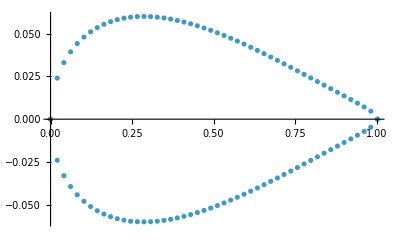

```mathematica
ListPlot[pts]
```

```mathematica
Norm/@(pts-RotateLeft[pts,1])
```

{0.0209858,0.0206029,0.0205761,0.0205675,0.0205643,0.0205632,0.0205629,0.0205628,0.0205626,0.0205622,0.0205615,0.0205604,0.0205589,0.0205569,0.0205544,0.0205516,0.0205482,0.0205445,0.0205403,0.0205357,0.0205307,0.0205254,0.0205197,0.0205138,0.0205077,0.0205015,0.0204951,0.0204888,0.0204825,0.0204765,0.0204708,0.0204657,0.0204613,0.020458,0.020456,0.0204559,0.0204583,0.0204638,0.0204738,0.0204896,0.0205136,0.0205493,0.0206022,0.0206822,0.0208072,0.0210162,0.0214095,0.0223617,0.03154,0.,0.03154,0.0223617,0.0214095,0.0210162,0.0208072,0.0206822,0.0206022,0.0205493,0.0205136,0.0204896,0.0204738,0.0204638,0.0204583,0.0204559,0.020456,0.020458,0.0204613,0.0204657,0.0204708,0.0204765,0.0204825,0.0204888,0.0204951,0.0205015,0.0205077,0.0205138,0.0205197,0.0205254,0.0205307,0.0205357,0.0205403,0.0205445,0.0205482,0.0205516,0.0205544,0.0205569,0.0205589,0.0205604,0.0205615,0.0205622,0.0205626,0.0205628,0.0205629,0.0205632,0.0205643,0.0205675,0.0205761,0.0206029,0.0209858,0.}